Background

```mathematica
coord ={t,r};
metric=({{r^2-1, 0}, {0, 1/(1-r^2)}});
```

```mathematica
$Assumptions= And[t∈Reals,r>0,r<1,ω∈Reals];
metricsign=-1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<diffgeo.m
```

```mathematica
EEstep1 = RicciTensor-1/2 RicciScalar*metric  + Λ* metric;
```

```mathematica
EEstep2 = EEstep1  /.Λ ->(d(d-1))/2/.d->1//Simplify
```

{{0,0},{0,0}}

```mathematica
Riemann;
```

```mathematica
contract[lower[Riemann,{4}]**lower[Riemann,{4}],{1,5},{2,6},{3,7},{4,8}]
```

4

Perturbation

```mathematica
Φ=Exp[-ⅈ*ω*t]*ϕ[r]
```

ⅇ^(-ⅈ t ω) ϕ[r]

```mathematica
f[r_]=((1-r^2)r^(d-1)ϕ'[r]);
SEstep1 = -r^(1-d)f'[r] //FullSimplify;
SEstep2 = Collect[SEstep1,{ϕ''[r],ϕ'[r],ϕ[r]},Simplify]+((l(l+d-2))/r^2-ω^2/(1-r^2))ϕ[r]
```

((l (-2+d+l))/r^2-ω^2/(1-r^2)) ϕ[r]+((1-d)/r+r+d r) ϕ'[r]+(-1+r^2) ϕ''[r]

```mathematica
Solution1=Values[DSolve[SEstep2==0,ϕ[r],r]][[1]][[1]]//FullSimplify
```

((-r)^-l (ⅈ r)^-d (-1+r^2)^(-1/2 ⅈ (ⅈ+ω)) (-r^2 C[2] Hypergeometric2F1[1/2 (2-l-ⅈ ω),1/2 (2-d-l-ⅈ ω),2-d/2-l,r^2]+(-1)^l ⅈ^d r^(d+2 l) C[1] Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2]))/(√(1-r^2))

```mathematica
SolutionR=(1-r^2)^((-ⅈ ω)/2)r^l Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2]
SolutionNR=(1-r^2)^((-ⅈ ω)/2)r^(2-d-l)Hypergeometric2F1[1/2 (2-l-ⅈ ω),1/2 (2-d-l-ⅈ ω),2-d/2-l,r^2]
```

r^l (1-r^2)^(-(ⅈ ω)/2) Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2]

r^(2-d-l) (1-r^2)^(-(ⅈ ω)/2) Hypergeometric2F1[1/2 (2-l-ⅈ ω),1/2 (2-d-l-ⅈ ω),2-d/2-l,r^2]

```mathematica
OriginBehaviour=Series[Solution1,{r,0,2}] //FullSimplify
```

r^(-d-l) (-ⅈ ⅇ^(1/2 π (-ⅈ (d+2 l)+ω)) C[2] r^2+O[r]^3)+r^l (ⅈ ⅇ^((π ω)/2) C[1]+(ⅈ ⅇ^((π ω)/2) (l (d+l)-ω^2) C[1] r^2)/(2 (d+2 l))+O[r]^3)

```mathematica
OriginBehavioutR=Series[SolutionR,{r,0,1}] //FullSimplify
OriginBehavioutNR=Series[SolutionNR,{r,0,1}] //FullSimplify
```

r^l (1+O[r]^2)

r^(-d-l) O[r]^2

```mathematica
BoundaryBehaviourR=Normal[Series[SolutionR,{r,1,0}]]//FullSimplify
```

(π (2-2 r)^(-(ⅈ ω)/2) Csch[π ω] Gamma[d/2+l] (1/(Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)] Gamma[-ⅈ ω])+(2-2 r)^(ⅈ ω)/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[ⅈ ω])))/ω

```mathematica
Solution1 /.C[2]->0//Simplify
Solution2 = Solution1 /.C[2]->0 //FullSimplify
Solution2/SolutionR//FullSimplify
```

(r^l (-1+r^2)^(-1/2 ⅈ (ⅈ+ω)) C[1] Hypergeometric2F1[1/2 (l-ⅈ ω),1/2 (d+l-ⅈ ω),d/2+l,r^2])/(√(1-r^2))

ⅈ ⅇ^((π ω)/2) r^l (1-r^2)^((ⅈ ω)/2) C[1] Hypergeometric2F1[1/2 (l+ⅈ ω),1/2 (d+l+ⅈ ω),d/2+l,r^2]

ⅈ ⅇ^((π ω)/2) C[1]

```mathematica
InftyBehaviourComprobation=Normal[Series[Solution2,{r,0,2}]] //FullSimplify
```

(ⅈ ⅇ^((π ω)/2) r^l (4 l+d (2+l r^2)+r^2 (l-ω) (l+ω)) C[1])/(2 (d+2 l))

```mathematica
BoundaryBehaviour=Normal[Series[Solution2,{r,1,0}]]/.C[1]->1//FullSimplify
```

ⅇ^((3 π ω)/2) π (2-2 r)^(-(ⅈ ω)/2) (-1+Coth[π ω]) Gamma[d/2+l] (-(2-2 r)^(ⅈ ω)/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[1+ⅈ ω])+1/(Gamma[1-ⅈ ω] Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)]))

```mathematica
Q1=-1/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[1+ⅈ ω])// FullSimplify
```

-1/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[1+ⅈ ω])

```mathematica
P1=1/(Gamma[1-ⅈ ω] Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)])//FullSimplify
```

1/(Gamma[1-ⅈ ω] Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)])

### Trying to obtain Quantization of Omega

```mathematica
alpha=Arg[P1]//FullSimplify
```

Arg[1/(Gamma[1-ⅈ ω] Gamma[1/2 (l+ⅈ ω)] Gamma[1/2 (d+l+ⅈ ω)])]

```mathematica
beta=Arg[Q1]//FullSimplify
```

Arg[-1/(Gamma[1/2 (l-ⅈ ω)] Gamma[1/2 (d+l-ⅈ ω)] Gamma[1+ⅈ ω])]

Sigma=0

```mathematica
OmegaQuantization={};
For[i=1, i<=400, i++,	
	Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[-20000ω]/.l->i/.d->2,{ω,0.00015},WorkingPrecision->100]]];
	AppendTo[OmegaQuantization,Value[[1]]];
]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantization]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantization,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantization];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantization]]/1000000]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

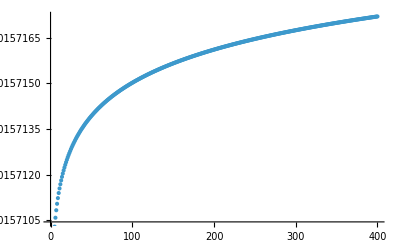

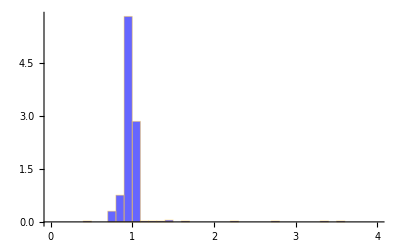

-Graphics-

```mathematica
ListPlot[OmegaQuantization]
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"}]
```

Sigma=2

```mathematica
OmegaQuantizationtwo={};
For[i=1, i<=1000, i++,
Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,2/Sqrt[i]],1] /.l->i/.d->2,{ω,0.00015},WorkingPrecision->100]]];
	OmegaQuantizationtwo=Append[OmegaQuantizationtwo,Value[[1]]]
]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantizationtwo]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationtwo,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantizationtwo];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

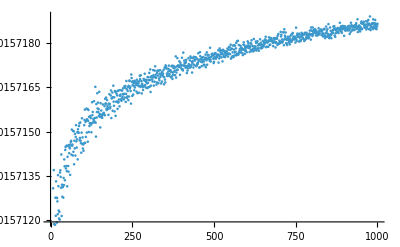

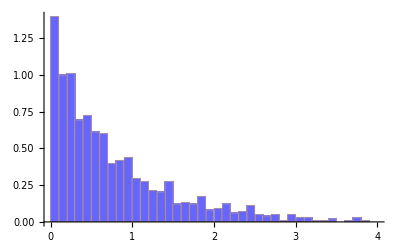

```mathematica
ListPlot[OmegaQuantizationtwo]
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantizationtwo]]/1000000]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

```mathematica
ChartStyle->{Opacity[0.6,Blue]}
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"}]
```

Sigma=0.025

```mathematica
OmegaQuantizationthree = {};
For[i=1, i<=400, i++,
	Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.016/Sqrt[i]],1] /.l->i/.d->2,{ω,0.00015},WorkingPrecision->100]]];
	OmegaQuantizationthree=Append[OmegaQuantizationthree,Value[[1]]]
]
```

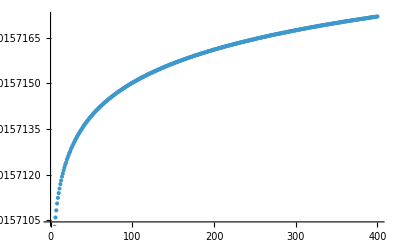

```mathematica
ListPlot[OmegaQuantizationthree]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantizationthree]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationthree,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantizationthree];
spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings25=spacings/meanSpacing;
```

```mathematica
histogram25=Histogram[normalizedSpacings25,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}];
```

```mathematica
wignerDyson[x_]:=(32/Pi^2) x^2 Exp[-(4/Pi) x^2];
wdPlot=Plot[wignerDyson[x],{x,0,3},PlotStyle->{Blue,Thick}];
```

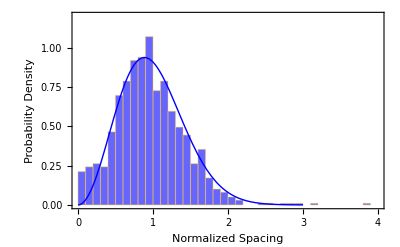

```mathematica
Show[histogram25,wdPlot,PlotRange->{{0,4},{0,1.2}},AxesOrigin->{0,0},Frame->True,FrameLabel->{"Normalized Spacing","Probability Density"},PlotLegends->{"Data","Wigner-Dyson"}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantizationthree]]/400]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

$Aborted

```mathematica
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"},PlotRange->{10^(-7),1}]
```

-Graphics-

### Estimation of beta

```mathematica
p[s_, β_]=(1+α)Gamma[(2+β)/(1+α)]^(1+β)/Gamma[(1+β)/(1+α)]^(2+β)s^β Exp[-s^(α+1)Gamma[(2+β)/(1+α)]^(1+α)/Gamma[(1+β)/(1+α)]^(1+α)]
```

ⅇ^(-s^(1+α) Gamma[(1+β)/(1+α)]^(-1-α) Gamma[(2+β)/(1+α)]^(1+α)) s^β (1+α) Gamma[(1+β)/(1+α)]^(-2-β) Gamma[(2+β)/(1+α)]^(1+β)

```mathematica
betaparameters={{},{},{}}
OmegaQuantizationBeta={}
For[k=2,k<=4,k++,
For[j=1,j<=10,j++,
For[i=1, i<=1000, i++,
	Value=Values[Quiet[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,(0.01+0.001*j)/Sqrt[i]],1] /.l->i /. d->k,{ω,0.00015},WorkingPrecision->100]]];
	OmegaQuantizationBeta[[j]][[k-1]]=Append[OmegaQuantizationBeta[[j]][[k-1]],Value[[1]]];
];
cumulativeDOS=Range[Length[OmegaQuantizationBeta[[j]][[k-1]]]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationBeta[[j]][[k-1]],cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];

unfoldedE=spline[OmegaQuantizationBeta[[j]][[k-1]]];
spacings=Differences[Sort[unfoldedE]];

meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;

{binEdges, binCounts}=HistogramList[normalizedSpacings,{0,4,.1},"PDF"];
binMidpoints = (binEdges[[1 ;; -2]] + binEdges[[2 ;; -1]]/2);
fit = NonlinearModelFit[Transpose[{binMidpoints, binCounts}],p[s, β]/.α->1,β,s];
betaparameters[[k-1]] = Append[betaparameters[[k-1]],Values[fit["BestFitParameters"]][[1]]];
Show[Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}],Plot[p[x,betaparameters[[k-1]][[j]]]/.α->1,{x,0,3},PlotStyle->{Blue,Thick}],PlotRange->{{0,4},{0,1.2}},AxesOrigin->{0,0},Frame->True,FrameLabel->{"Normalized Spacing","Probability Density"},PlotLegends->{"Data","Wigner-Dyson"}]
]
]
cumulativebeta = cumulativebeta +
```

```mathematica
betaparameters
```

{{1.92088,1.57964,1.44288,1.47436,1.02637,1.03667,0.983778,0.870821,0.677094,0.585876},{1.91824,1.68099,1.69228,1.16741,0.906794,0.997839,0.902077,0.923394,0.57881,0.789744},{1.51502,1.57526,1.35327,1.51906,1.05849,0.885277,0.954872,0.84654,0.719119,0.657449}}

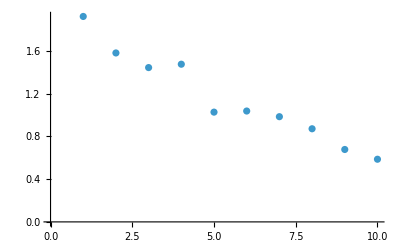

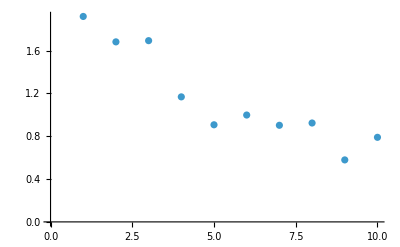

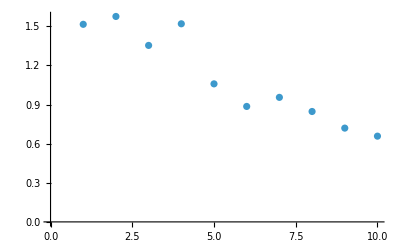

```mathematica
Show[ListPlot[betaparameters[[1]]],FrameLabel->{"β","σ"}]
Show[ListPlot[betaparameters[[2]]],FrameLabel->{"β","σ"}]
Show[ListPlot[betaparameters[[3]]],FrameLabel->{"β","σ"}]
```